## Test Systems

A collection of standard (and less standard systems)

### Smoothed Sprott Jerk systems from ??

```mathematica
Clear[Sprott,Di,Rd,Sa,Sg,He]
Sprott=<|1-><|"fun":>-a ypp+b yp-c y+d yp^2,"par"->{2.017,0,1,1,50},"IC"->{0,0,1},"lam"->{0.055,0,-2.072}|>,2-><|"fun":>a ypp-b yp+c y+d y^2,"par"->{0,2.8,1,1,50},"IC"->{-0.5,-1,1},"lam"->{0.002,0,-0.002}|>,3-><|"fun":>-a ypp-b yp+c y+d (y^2-1),"par"->{0.44,2,0,1,50},"IC"->{0,0,0},"lam"->{0.105,0,-0.545}|>,4-><|"fun":>-a ypp-b yp+c y+d y^2,"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"lam"->{0.094,0,-0.594}|>,5-><|"fun":>a ypp-b yp+c y+d (Abs[y]-1),"par"->{0,2,0,1,50},"IC"->{-1,-1,1},"lam"->{0.003,0,-0.003}|>,6-><|"fun":>-a ypp-b yp+c y+d (Abs[y]-1),"par"->{0.6,1,0,1,50},"IC"->{0,0,0},"lam"->{0.036,0,-0.636}|>,7-><|"fun":>-a ypp-b yp+c y-d (Di[y]-1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0},"lam"->{0.042,0,-0.342}|>,8-><|"fun":>-a ypp-b yp+c y-d (Rd[y]+1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0},"lam"->{0.042,0,-0.342}|>,9-><|"fun":>a ypp-b yp+c y-d (Di[y]-1),"par"->{0,2.9,0.7,1,50},"IC"->{0,-0.5,0.5},"lam"->{0.003,0,-0.003}|>,10-><|"fun":>a ypp-b yp+c y-d (Rd[y]+1),"par"->{0,2.9,0.7,1,50},"IC"->{0,0.5,-0.5},"lam"->{0.003,0,-0.003}|>,11-><|"fun":>-a ypp-b yp-c y+d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"lam"->{0.152,0,-0.652}|>,12-><|"fun":>-a ypp-b yp+c y-d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"lam"->{0.601,0,-1.101}|>,13-><|"fun":>-a ypp-b yp-c y+d He[m][y],"par"->{0.7,1,1,1,50},"IC"->{0,1,0},"lam"->{0.085,0,-0.785}|>,14-><|"fun":>-a ypp-b yp-c y+d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0},"lam"->{0.072,0,-0.472}|>,15-><|"fun":>-a ypp-b yp+c y-d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0},"lam"->{0.091,0,-0.491}|>,16-><|"fun":>-a ypp-b yp-c y+d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0},"lam"->{0.128,0,-0.318}|>,17-><|"fun":>-a ypp-b yp+c y-d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0},"lam"->{0.067,0,-0.257}|>,18-><|"fun":>a ypp-b yp+c y-d y^3,"par"->{0,3.7,1,1,50},"IC"->{0,0.5,1},"lam"->{0.002,0,-0.002}|>,19-><|"fun":>-a ypp+b yp-c y-d yp^3,"par"->{0.6,2.8,1,1,50},"IC"->{0,1,0},"lam"->{0.034,0,-0.634}|>,20-><|"fun":>-a ypp-b yp+c y-d y^3,"par"->{0.7,1,1,1,50},"IC"->{0,1,0},"lam"->{0.138,0,-0.838}|>,21-><|"fun":>-a ypp-b yp-c y+d y^3,"par"->{0.35,1,1,1,50},"IC"->{0,1,0},"lam"->{0.082,0,-0.432}|>,22-><|"fun":>-a ypp-b yp+c y+d Sin[y],"par"->{0.2,1,0,1,50},"IC"->{0,1,0},"lam"->{0.123,0,-0.323}|>|>
(* Compute Derivtives automatically *)
NewSprott=Map[Function[entry,With[{der=D[entry["fun"],{{y,yp,ypp}}]},Append[entry,"der":>der]]],Sprott];
DerSub={Abs'[y]->Absp[y],Di'[y]->Dip[y],Rd'[y]->Rdp[y],Sa'[y]->Sap[y],Sg[m]'[y]->Sgp[m][y],He[m]'[y]->He[m][y]};
NewSprott=NewSprott/.DerSub;
```

<|1→<|fun:>-a ypp+b yp-c y+d yp^2,par→{2.017,0,1,1,50},IC→{0,0,1},lam→{0.055,0,-2.072}|>,2→<|fun:>a ypp-b yp+c y+d y^2,par→{0,2.8,1,1,50},IC→{-0.5,-1,1},lam→{0.002,0,-0.002}|>,3→<|fun:>-a ypp-b yp+c y+d (y^2-1),par→{0.44,2,0,1,50},IC→{0,0,0},lam→{0.105,0,-0.545}|>,4→<|fun:>-a ypp-b yp+c y+d y^2,par→{0.5,1,1,1,50},IC→{0,1,0},lam→{0.094,0,-0.594}|>,5→<|fun:>a ypp-b yp+c y+d (Abs[y]-1),par→{0,2,0,1,50},IC→{-1,-1,1},lam→{0.003,0,-0.003}|>,6→<|fun:>-a ypp-b yp+c y+d (Abs[y]-1),par→{0.6,1,0,1,50},IC→{0,0,0},lam→{0.036,0,-0.636}|>,7→<|fun:>-a ypp-b yp+c y-d (Di[y]-1),par→{0.3,0.3,0,1,50},IC→{0,0,0},lam→{0.042,0,-0.342}|>,8→<|fun:>-a ypp-b yp+c y-d (Rd[y]+1),par→{0.3,0.3,0,1,50},IC→{0,0,0},lam→{0.042,0,-0.342}|>,9→<|fun:>a ypp-b yp+c y-d (Di[y]-1),par→{0,2.9,0.7,1,50},IC→{0,-0.5,0.5},lam→{0.003,0,-0.003}|>,10→<|fun:>a ypp-b yp+c y-d (Rd[y]+1),par→{0,2.9,0.7,1,50},IC→{0,0.5,-0.5},lam→{0.003,0,-0.003}|>,11→<|fun:>-a ypp-b yp-c y+d Sg[m][y],par→{0.5,1,1,1,50},IC→{0,1,0},lam→{0.152,0,-0.652}|>,12→<|fun:>-a ypp-b yp+c y-d Sg[m][y],par→{0.5,1,1,1,50},IC→{0,1,0},lam→{0.601,0,-1.101}|>,13→<|fun:>-a ypp-b yp-c y+d He[m][y],par→{0.7,1,1,1,50},IC→{0,1,0},lam→{0.085,0,-0.785}|>,14→<|fun:>-a ypp-b yp-c y+d Sa[y],par→{0.4,1,1,2,50},IC→{0,1,0},lam→{0.072,0,-0.472}|>,15→<|fun:>-a ypp-b yp+c y-d Sa[y],par→{0.4,1,1,2,50},IC→{0,1,0},lam→{0.091,0,-0.491}|>,16→<|fun:>-a ypp-b yp-c y+d Tanh[y],par→{0.19,1,1,2,50},IC→{0,1,0},lam→{0.128,0,-0.318}|>,17→<|fun:>-a ypp-b yp+c y-d Tanh[y],par→{0.19,1,1,2,50},IC→{0,1,0},lam→{0.067,0,-0.257}|>,18→<|fun:>a ypp-b yp+c y-d y^3,par→{0,3.7,1,1,50},IC→{0,0.5,1},lam→{0.002,0,-0.002}|>,19→<|fun:>-a ypp+b yp-c y-d yp^3,par→{0.6,2.8,1,1,50},IC→{0,1,0},lam→{0.034,0,-0.634}|>,20→<|fun:>-a ypp-b yp+c y-d y^3,par→{0.7,1,1,1,50},IC→{0,1,0},lam→{0.138,0,-0.838}|>,21→<|fun:>-a ypp-b yp-c y+d y^3,par→{0.35,1,1,1,50},IC→{0,1,0},lam→{0.082,0,-0.432}|>,22→<|fun:>-a ypp-b yp+c y+d Sin[y],par→{0.2,1,0,1,50},IC→{0,1,0},lam→{0.123,0,-0.323}|>|>

Define the  functions and derivatives.

```mathematica
Clear[Di,Dip,Rd,Rdp,Sa,Sap,Sg,Sgp,He,HEp,Absp,m]
Di[u_]:=Max[u,0]; Dip[u_]:=If[u>0,1,0]
Rd[u_]:=Min[u,0]; Rdp[u_]:=If[u<0,1,0]
Sa[u_]:=Piecewise[{ {-1, u<-1},{u, -1<u<1},{1,True}}]; Sap[u_]:=If[Abs[u]<1,1,0]
Sg[m_][u_]:=Tanh[m u]; Sgp[m_][u_]:=m Sech[m u]^2
He[m_][u_]:=(1+Tanh[m u])/2; Hep[m_][u_]:=1/2 m Sech[m u]^2
Absp[u_]:= If[u<0,-1,1]

Do[
fSprott[k,{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={yp,ypp,Sprott[k]["fun"]};
dyfSprott[k,{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={{0,1,0},{0,0,1},Sprott[k]["dery"]};
fSprott[k][{y_,yp_,ypp_}]=fSprott[k,Sprott[k]["par"]][{y,yp,ypp}];
dyfSprott[k][{y_,yp_,ypp_}]=dyfSprott[k,Sprott[k]["par"]][{y,yp,ypp}],
{k,22}]
Protect[Sprott, fSprott,dyfSprott];
```

### Rosseller and Lorenz Systems

```mathematica
Clear[Ross,dRoss,HRoss,dHRoss,Lor, dLor]
(* Rossler *)
(* {a,b,c} = {0.2,0.2,5.7} *)
Ross[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x+a y,b+z (x-c)}
dRoss[{a_,b_,c_}][{x_,y_,z_}]:={{0,-1,-1},{1,a,0},{z,0,x-c}}
(* Hyperchaotic Rossler *)
(* {a,b,c,d}={0.25,3,0.5,0.05} *)
HRoss[{a_,b_,c_,d_}][{x_,y_,z_,w_}]:={-y-z,x+a y+w,b+x z,-c z+d w}
dHRoss[{a_,b_,c_,d_}][{x_,y_,z_,w_}]:={{0,-1,-1,0},{1,a,0,1},{z,0,x,0},{0,0,-c,d}}
(*Lorenz*)
(* {sigma, rho, beta}={10,28,8/3} *)
Lor[{sigma_,rho_,beta_}][{x_,y_,z_}]:={sigma (y-x),x (rho-z)-y,x y-beta z};
dLor[{sigma_,rho_,beta_}][{x_,y_,z_}]:={{-sigma,sigma,0},{rho-z,-1,-x},{y,x,-beta}};
```

## Visualization Tool

I made a tool to scan through a range of parameters to look for one around and twice around solutions and other interesting things.  It takes defaults and ranges from the pre-defined Sprott functions.   It is not pretty yet.   It is hard to get a balance between running long enough to get near the attractor and seeing the dynamics on the attractor.

```mathematica
Clear[k,p,y0,f,a,b,c,d,m,y,yp,ypp,ySol]
k=12;Sys=Sprott[k];
{a0,b0,c0,d0,m0}=Sys["par"];y0=Sys["IC"];λs=Sys["lam"];
τ=-1/Min[λs];MulMax=100; TMax= MulMax*τ;
{k,Sprott[k]["fun"]}
Manipulate[
yExplore=NDSolveValue[{
y'[t]==fSprott[k,{a,b,c,d,m0}][y[t]],y[0]==y0},y,{t,0, TMax}];
ParametricPlot3D[yExplore[t],{t,0.7 TMax, TMax},PlotRange->All,PlotLabel->k,PlotPoints->100],
{{a,a0},0,Max[2 a0,1], a0/100.0,Appearance->"Open"},
{{b,b0},0,Max[2 b0,1], b0/100.0,Appearance->"Open"},
{{c,c0},0,Max[2 c0,1], c0/100.0,Appearance->"Open"},
{{d,d0},0,Max[2 d0,1], d0/100.0,Appearance->"Open"},ControlPlacement->Left, ContinuousAction->False]
```

{12,c y-b yp-a ypp-d Tanh[m y]}

## Basic Solvers

Systems are all defined by an autonomous ODE 
	y'=f(y) 
with f : ℝ^n → ℝ^n and a provided derivative df : ℝ^n → ℝ^(n×n) for the sensitivity computation
	J'=df(y).J

The basic solver simultaneously approximates 
	y'=f(y)  and J'=df(y).J
from an initial condition y(0)=y0 and J(0)=Id_n.  The solver returns a list containing interpolating functions for y and J.

```mathematica
yJSolve[{f_,df_},y0_,TMax_]:=Module[{n=Length[y0],Id,y,J},
Id=IdentityMatrix[n];
 NDSolveValue[{
y'[t]==f[y[t]],y[0]==y0,
J'[t]==df[y[t]].J[t],J[0]==Id},{y,J},{t,0, TMax}]
]
```

Tests

```mathematica
p={0.2,0.2,5.7};
y0={1,2,3}; TMax=123;
{ySol,JSol}=yJSolve[{Ross[p],dRoss[p]},y0,TMax];
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All]
```

-Graphics3D-

```mathematica
p={0.25,3,0.5,0.05};
y0={-6.,0.,0.5,14.}; TMax=123;
{ySol,JSol}=yJSolve[{HRoss[p],dHRoss[p]},y0,TMax];
Plot[{ySol[t]⟦1⟧,ySol[t]⟦2⟧,ySol[t]⟦3⟧,ySol[t]⟦4⟧},{t,0, TMax},PlotRange->All];
TabView[{
ParametricPlot3D[ySol[t]⟦{1,2,3}⟧,{t,0,TMax},PlotRange->All,PlotPoints->100],
ParametricPlot3D[ySol[t]⟦{1,2,4}⟧,{t,0,TMax},PlotRange->All,PlotPoints->100],
ParametricPlot3D[ySol[t]⟦{1,3,4}⟧,{t,0,TMax},PlotRange->All,PlotPoints->100],
ParametricPlot3D[ySol[t]⟦{2,3,4}⟧,{t,0,TMax},PlotRange->All,PlotPoints->100]}]
```

1234

## Lyapunov Solvers

Systems are all defined by the autonomous ODEs 
	y'=f(y)  and J'=df(y).J
the naive Lyapunov computation tracks the singular values of J using the basic tracker.  As we know this rapidly develops problems because the small singular values rapidly become negligible compared to the large singular values.  The Lyapunov exponents are the exponential growth and decay visible in the system.  The numerical value we see in the short run depends on the IC.  Theoretically in the long run they do not depend on the IC. 
“In theory there is no difference between theory and practice. In practice there is.”

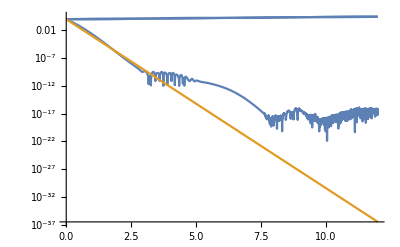

```mathematica
SetOptions[SingularValueList,Tolerance->0];
p= {0.2,0.2,5.7}; y0={1,2,3};TMax=12;
{ySol,JSol}=yJSolve[{Ross[p],dRoss[p]},y0,TMax];
LogPlot[{
SingularValueList[JSol[t]],
E^(-7 t)},{t,0, TMax}]
```

If we want to see this effect we need to be able to measure the compression and expansion over longer time scales.  The simplest version of this just rescales the columns of J at regular time intervals. It does this with a periodic QR decomposition which dumps the stretches of the columns.  The standard version does the diagonals of the upper triangular R matrix.

```mathematica
Clear[LyapunovStretches]
LyapunovStretches[{f_,df_},y0_,{dt_,TMax_}]:= Module[{n=Length[y0],Q0,R},
(*Q0=QRDecomposition[RandomReal[{-1,1},{n,n}]]⟦1⟧ᵀ;*)
Q0=IdentityMatrix[n];
(* returns a list {{y,J}, {Stretches}} *)
Reap[
NDSolveValue[
{y'[t]==f[y[t]], J'[t]==df[y[t]].J[t], y[0]==y0, J[0]==Q0, 
WhenEvent[Mod[t,dt]==0, {Q0, R}=QRDecomposition[J[t]];Sow[Diagonal[R]];J[t]->Q0ᵀ]},
{y,J},{t,0, TMax}]
]
]

LyapunovStretchesSVD[{f_,df_},y0_,{dt_,TMax_}]:= Module[{n=Length[y0],Q0,R},
(*Q0=QRDecomposition[RandomReal[{-1,1},{n,n}]]⟦1⟧ᵀ;*)
Q0=IdentityMatrix[n];
(* returns a list {{y,J}, {Stretches}} *)
Reap[
NDSolveValue[
{y'[t]==f[y[t]], J'[t]==df[y[t]].J[t], y[0]==y0, J[0]==Q0, 
WhenEvent[Mod[t,dt]==0, {Q0, R}=QRDecomposition[J[t],Pivoting->False];Sow[SingularValueList[R]];J[t]->Q0ᵀ]},
{y,J},{t,0, TMax}]
]
]
```

```mathematica
SetPrecision[ySol[TMax],2]
```

{3.1,5.4,4.9}

```mathematica
SetOptions[SingularValueList,Tolerance->0];
p= {0.2,0.2,5.7}; y0={3.1,5.4,4.9};TMax=6;
dt =0.2;{{ySol,JSol},{DataR}}=LyapunovStretches[{Ross[p],dRoss[p]},y0,{dt,TMax}];
{{ySol,JSol},{DataS}}=LyapunovStretchesSVD[{Ross[p],dRoss[p]},y0,{dt,TMax}];
lambda=-5.1;
TabView[{
"3D"->ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All],
"Scaling"->LogPlot[{SingularValueList[JSol[t]],Exp[lambda*Mod[t,dt]]},{t,0, TMax}]
}]
```

12

The scalings are.

```mathematica
TableForm[DataRᵀ,TableHeadings->Automatic]
TableForm[DataSᵀ,TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
1 | -1.04817 | 0.875555 | 0.924287 | 1.00213 | 1.0276 | 1.03641 | 1.04017 | -1.04033 | 1.03741 | 1.03216 | 1.02544 | 1.01813 | 1.0111 | 1.00516 | 1.00113 | 0.999729 | 1.00147 | 1.0064 | 1.01388 | 1.02254 | 1.0307 | 1.03695 | -1.04088 | 1.04265 | 1.03792 | 1.06687 | 1.62617 | 1.66817 | -0.853583 | 0.524432
2 | -1.04084 | 1.03319 | 1.0177 | 1.0123 | 1.00815 | 1.00323 | 1.00021 | -1.00017 | 1.00302 | 1.00815 | 1.01476 | 1.02203 | 1.02913 | 1.03518 | 1.0393 | 1.04066 | 1.03871 | 1.03338 | 1.02532 | 1.0158 | 1.0061 | 0.996902 | -0.991094 | 1.03295 | 1.42111 | 2.09194 | 1.21298 | 0.734929 | 0.896746 | 1.14716
3 | 0.467215 | 0.400389 | 0.287366 | 0.203812 | 0.155276 | 0.122972 | 0.100662 | 0.0857202 | 0.0765226 | 0.0720752 | 0.0719565 | 0.0763297 | 0.0860367 | 0.102801 | 0.129574 | 0.17104 | 0.234232 | 0.329047 | 0.468149 | 0.66534 | 0.931261 | 1.26552 | 1.64048 | 1.91032 | 1.56273 | 1.03493 | 1.00141 | 1.12963 | -1.09909 | 0.865609

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
1 | 1.05161 | 1.04066 | 1.04067 | 1.04067 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.04068 | 1.06092 | 1.29173 | 1.64237 | 1.9796 | 2.20252 | 2.24022 | 2.21698 | 2.17911 | 1.73216 | 1.17685
2 | 1.04061 | 0.991735 | 0.998821 | 1.00329 | 1.00387 | 1.0035 | 1.00309 | 1.00279 | 1.00259 | 1.00248 | 1.00246 | 1.00252 | 1.00268 | 1.00297 | 1.00344 | 1.00416 | 1.0053 | 1.00721 | 1.01079 | 1.0195 | 1.04067 | 1.04067 | 1.04067 | 1.04067 | 1.04068 | 1.04068 | 1.04069 | 1.04068 | 1.04064 | 1.04063
3 | 0.465789 | 0.350947 | 0.260053 | 0.198026 | 0.153979 | 0.122434 | 0.100323 | 0.0854676 | 0.0763155 | 0.0718893 | 0.0717729 | 0.0761298 | 0.085796 | 0.102481 | 0.129104 | 0.170283 | 0.232899 | 0.326478 | 0.462653 | 0.651378 | 0.874675 | 0.973181 | 0.990152 | 0.998687 | 1.00563 | 0.990753 | 0.856149 | 0.610701 | 0.466724 | 0.425226

The traditional thing to do is to take logs of the R stretches, add them up which gives you the logs of the total cumulative stretches and then average.  It is traditional to not include the first few transient stretches in the average.

```mathematica
LyapunovExps[{f_,df_},y0_,{dt_,TMax_},nSkip_]:= Module[{RStretches},
RStretches=Drop[LyapunovStretches[{f,df},y0,{dt,TMax}]⟦2,1⟧,nSkip];
Mean[Log[Abs[RStretches]]]/dt
]
p= {0.2,0.2,5.7}; y0=y0={3.1,5.4,4.9};;TMax=123;
dt =0.1;nSkip=7;
LyapunovExps[{Ross[p],dRoss[p]},y0,{dt,TMax},nSkip]
```

{0.0796861,0.00295402,-5.40299}

### Continuous QR Lyapunov Computation

A standard (but quite fancy) trick to avoid stopping the simulation all the time and doing a QR decomposition is to build the ODEs for J(t)=Q(t).R(t) where 
	Qᵀ.Q=Id
and we really want to track only the diagonals of the upper triangular factor R. From our product rule
	J'=Q'.R+Q.R'  and (Q')ᵀ.Q+Qᵀ.Q'=0
Another way to say the second is that W=Qᵀ.Q' is skew i.e. Wᵀ=-W .   If we plug into our ODE J'=A.J we get 
	Q'.R+Q.R'=A.Q.R
If we multiply by Qᵀ we get
	Qᵀ.Q'.R+Qᵀ.Q.R'=Qᵀ.A.Q.R
If we define B=Qᵀ.A.Q and L=tril(B,-1) and Ω=L-Lᵀ and T=B-Ω then  
	Q' | = | Q.(L-Lᵀ)
R' | = | T.R
This decomposition works because R is upper triangular and the strictly lower triangular part of R' is zero!   If we only want the diagonal of R then we do not need to track the whole of R.  We can track logarithms of the diagonals to avoid catastrophic growth and decay

## Poincare Sections

Restrict attention to hyperplane sections (p-p_0).n=0.
	In 2D this is a line perpendicular to the normal n through p_0.
	In 3D this is a plane perpendicular to the normal n through p_0.
	In 4D this is a hyperplane perpendicular to the normal n through p_0.
The advantage of a plane is that it is parameterized by a set of n-1 directions.  These tangent directions are perpendicular to the normal n. We can choose them to be orthogonal.

T is going to be an n×(n-1) matrix of the tangent vectors T=[t_1|t_2|…|t_(n-1)].  So Tᵀ.T=Id_(n-1) and Tᵀ.n=0_(n-1).  The section plane in all our codes is going to be described by the list
	{p0,n,T}
Switching n→-n gives the same hyperplane with the opposite orientation.  The mapping from the parameter space x∈ℝ^(n-1) to the ambient space is  x->T x + p0.  The projection from the ambient space y∈ℝ^n to the parameter space is y→Tᵀ(y-p0).  You can (and should) check that this matches the use of the word projector in other math contexts.

“PoincarePoints” takes the function f and initial condition y0, the parameters {p0,n,T} of the plane and a capture range {TMin,TMax} and returns a list of the the points on the plane in the ambient space together with a list of the parameters for those points.

```mathematica
Clear[PoincarePoints]
PoincarePoints[f_,y0_,{p0_,n_,T_},{TMin_, TMax_}]:=Module[{y,SecPts},
SecPts=Reap[ NDSolveValue[{y'[t]==f[y[t]],y[0]==y0,
WhenEvent[n.(y[t]-p0)>0,If[t>TMin, Sow[y[t]]]]},{y},{t,0, TMax}]]⟦2,1⟧;
{SecPts, Table[Tᵀ.(SecPts⟦i⟧-p0),{i,Length[SecPts]}]}
]
```

```mathematica
{TMin,TMax}={12,123};
p={0.2,0.2,5.7}; y0={1,2,3};
{ySol,JSol}=yJSolve[{Ross[p],dRoss[p]},y0,TMax];
T=({{0, 0}, {1, 0}, {0, 1}});n={-1,0,0}; p0={5.7,0,0};
{SecPts,ProjSecPts}=PoincarePoints[Ross[p],y0,{p0,n,T},{TMin,TMax}];
TabView[{
"3D"->Show[
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All],
ListPointPlot3D[SecPts,PlotStyle->Red],AxesLabel->{"y_1","y_2","y_3"}],
"2D"->ListPlot[ProjSecPts,PlotStyle->Red,AxesLabel->{"x_1","x_2"}]
}
]
```

12

Lets test on the Hyper Chaos system.

```mathematica
p={0.25,3,0.5,0.05};
y0={-6.,0.,0.5,14.}; {TMin,TMax}={12,123};
T=({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}, {0, 0, 1}});n={0,0,1,0}; p0={1,2,3,4};
{ySol,JSol}=yJSolve[{HRoss[p],dHRoss[p]},y0,TMax];
{SecPts,ProjSecPts}=PoincarePoints[HRoss[p],y0,{p0,n,T},{TMin,TMax}];


Show[
ParametricPlot3D[Tᵀ.(ySol[t]-p0),{t,0,TMax},PlotRange->All,PlotPoints->100,
AxesLabel->{"x_1","x_2","x_3"}],
ListPointPlot3D[ProjSecPts,PlotStyle->Red]]
```

-Graphics3D-

More points and no curve.

```mathematica
p={0.25,3,0.5,0.05};
y0={-6.,0.,0.5,14.}; {TMin,TMax}={12,12345};
T=({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}, {0, 0, 1}});n={0,0,1,0}; p0={1,2,3,4};
{SecPts,ProjSecPts}=PoincarePoints[HRoss[p],y0,{p0,n,T},{TMin,TMax}];
ListPointPlot3D[ProjSecPts,PlotStyle->PointSize[0.005],PlotRange->All,
AxesLabel->{"x_1","x_2","x_3"}]
```

Same parameters but a different plane!

```mathematica
p={0.25,3,0.5,0.05};
y0={-6.,0.,0.5,14.}; {TMin,TMax}={12,12345};
T=({{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {0, 0, 1}});n={1,0,0,0}; p0={1,2,3,4};
{SecPts,ProjSecPts}=PoincarePoints[HRoss[p],y0,{p0,n,T},{TMin,TMax}];
ListPointPlot3D[ProjSecPts,PlotStyle->PointSize[0.005],PlotRange->All,
AxesLabel->{"x_1","x_2","x_3"}]
```

-Graphics3D-

## Poincare Maps and Derivatives.

As before, the section hyperplane in ℝ^n is described by {p0,n,T}  with n.n=1, Tᵀ.T=Id_(n-1), and Tᵀ.n=0_(n-1).  As before, the flow is described by f:ℝ^n→ℝ^n and its derivative df:ℝ^n→ℝ^(n×n). The plan is to take a single step from the section back to the section. For an initial condition
	y(0)=y0=p0+Tx0
on the plane described by the parameters x0.  The function τyJ gives the the first positive crossing time of the orbit, along with the point y(τ), and full sensitivity J(τ).  TMin>0 but small is to prevent premature triggering of the condition because y0 is on (or at very-very near) the plane.  I made sure to start this on a positive crossing.

```mathematica
Clear[τyJSolve]
τyJSolve[{f_,df_},y0_,{p0_,n_,T_},{TMin_, TMax_}]:=Module[
{y,J,τyJ},
NDSolveValue[{y'[t]==f[y[t]],y[0]==y0,
J'[t]==df[y[t]].J[t], J[0]==IdentityMatrix[Length[y0]],
WhenEvent[And[n.(y[t]-p0)>0,t>TMin],
{τyJ={t,y[t],J[t]},"StopIntegration"}]
},{y},{t,0, TMax}];
τyJ
]
```

As always test.

```mathematica
{TMin,TMax}={10^-6,123};
p={0.2,0.2,5.7}; 
T=({{0, 0}, {1, 0}, {0, 1}});n={-1,0,0}; p0={5.7,0,0};
x0={1.1,2.2}; y0=p0+T.x0;
{τVal,yVal,JVal}=τyJSolve[{Ross[p],dRoss[p]},y0,{p0,n,T},{TMin,TMax}]
{ySol,JSol}=yJSolve[{Ross[p],dRoss[p]},y0,τVal];
TabView[{
"3D"->Show[
ParametricPlot3D[ySol[t],{t,0, τVal}],
ParametricPlot3D[p0+T.{x1,x2},{x1,0,7},{x2,0,7}]],
"n.(y(t)-p0)"->Plot[n.(ySol[t]-p0),{t,0, τVal},PlotRange->All]}]
```

{6.57439,{5.7,4.56058,3.60672},{{-0.560199,-1.68846,-0.101332},{0.156776,1.1957,0.254617},{3.72904,2.18538,-2.15822}}}

Lets test on the Hyper Chaos system. We are not finding periodic solutions yet!

```mathematica
{TMin,TMax}={10^-6,123};
p={0.25,3,0.5,0.05};
T=({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}, {0, 0, 1}});n={0,0,1,0}; p0={-6.,0.,0.5,14.};
x0={1,-3,4}; y0=p0+T.x0;
{τVal,yVal,JVal}=τyJSolve[{HRoss[p],dHRoss[p]},y0,{p0,n,T},{TMin,TMax}]
{ySol,JSol}=yJSolve[{HRoss[p],dHRoss[p]},y0,τVal];
TabView[{
"3D"->ParametricPlot3D[Tᵀ.(ySol[t]-p0),{t,0, τVal},PlotRange->All],
"n.(y(t)-p0)"->Plot[n.(ySol[t]-p0),{t,0, τVal},PlotRange->All]
}]
```

{5.78277,{-3.56222,-17.9104,0.5,23.2918},{{1.78826,1.04547,-0.338896,0.464854},{-0.900007,1.47426,0.373998,-1.14559},{0.108449,0.0770295,-0.0190734,0.0210657},{-0.0573964,0.0193513,-0.126021,1.36006}}}

12

Now we want to have the map from the input parameterization x∈ℝ^(n-1) to the output parametrization Tᵀ.(y-p0)∈ℝ^(n-1).  As we saw before (in 3D) there are two things we need to address.  The first is that the flight time τ depends on the input parameterization x.  The second is that J(τ) is n×n and the derivative with respect to x0 of the parameterized first return map
	x->Tᵀ.(ySol(τ)-p0)
where y(0)=p0+T.x0 is an (n-1)×(n-1) matrix.  Rederivation for the thrid time coming!

The recipe (using the Kronecker/outer product notation) is 
	Tᵀ(I-(f⊗n)/(f.n))J T
All I really need to do is add this onto the τ, y, J solver. I am going to return a list of 
	{τ,y,J,x,∂_x x}.
How would you test this?

```mathematica
{n1,v1}=RandomReal[{-1,1},{2,3}];n2={n1}ᵀ; v2={v1}ᵀ;
MatrixForm[n2.v2ᵀ ]
MatrixForm[KroneckerProduct[n1,v1]]
```

(0.237586 | 0.0191241 | -0.336387
0.0978922 | 0.00787967 | -0.138601
-0.211262 | -0.0170052 | 0.299115)

(0.237586 | 0.0191241 | -0.336387
0.0978922 | 0.00787967 | -0.138601
-0.211262 | -0.0170052 | 0.299115)

```mathematica
τyJxDSolve[{f_,df_},x0_,{p0_,n_,T_},{TMin_, TMax_}]:=Module[
{Id=IdentityMatrix[Length[n]],y0=p0+T.x0,τ,y,J,v},
{τ,y,J}=τyJSolve[{f,df},y0,{p0,n,T},{TMin, TMax}];
v=f[y];
{τ,y,J,Tᵀ.(y-p0),Tᵀ.(Id-KroneckerProduct[n,v]/(v.n)).J.T}
]
```

Test

```mathematica
{TMin,TMax}={10^-6,123};
p={0.2,0.2,5.7}; 
T=({{0, 0}, {1, 0}, {0, 1}});n={-1,0,0}; p0={5.7,0,0};
x0={1.1,2.2}; y0=p0+T.x0;
{τVal,yVal,JVal,xVal,DVal}=τyJxDSolve[{Ross[p],dRoss[p]},x0,{p0,n,T},{TMin,TMax}];
Map[MatrixForm,{JVal,DVal}]
```

{(-0.560199 | -1.68846 | -0.101332
0.156776 | 1.1957 | 0.254617
3.72904 | 2.18538 | -2.15822),(1.1957 | 0.254617
2.18538 | -2.15822)}

How would I check the derivative is correct!

## Finding Periodic Solutions on Sections

For the twice around system we want to solve
	q_2 | = | p(q_1)
q_1 | = | p(q_2)⟹ | p(q_1)-q_2 | = | 0
p(q_2)-q_1 | = | 0⟹g(q)=0
where 
	q=(q_1
q_2) and g(q)=(p(q_1)-q_2
p(q_2)-q_1) and Dg(q)=(Dp(q_1) | -I_n
-I_n | Dp(q_2))  
Newton’s method (with q^k indicating the k^th iteration of the stack) is
	q^(k+1)=q^k-(Df(q^k))^-1 g(q^k).

The first thing I need is a test problem.  This sure looks like a twice around solution! It is not perfect! The aim is to run a Newton solver to make it better

```mathematica
p={a,b,c}={0.2,0.2,2.8}; y0={1,2,3}; TMax=123;
T=({{0, 0}, {1, 0}, {0, 1}}); n={-1,0,0}; p0={c,0,0};
{ySol,JSol}=yJSolve[{Ross[p],dRoss[p]},y0,TMax];
yEnd=ySol[TMax];
{qpts,xpts}=PoincarePoints[Ross[p],yEnd,{p0,n,T},{10^-6, 30}];
Show[
ParametricPlot3D[ySol[t],{t,0.9TMax,TMax}],
ParametricPlot3D[p0+T.{x1,x2},{x1,1,3},{x2,2,4.5}],
ListPointPlot3D[qpts,PlotStyle->Black]
]
TabView[{
"q"->TableForm[qpts,TableHeadings->Automatic],
"x"->TableForm[xpts,TableHeadings->Automatic]}]
```

-Graphics3D-

12

I am going to build it slowly.  Something is wrong here!!

```mathematica
p={a,b,c}={0.2,0.2,2.8}; y0={1,2,3}; TMax=123;
T=({{0, 0}, {1, 0}, {0, 1}}); n={-1,0,0}; p0={c,0,0};
f=Ross[p];df=dRoss[p];
TMin=10^-8;TMax=20;
{q1,q2}={{2.3,4.9},{2.6,2.5}};
(* Build the bits I need *)
Id=IdentityMatrix[2];
{p1,Dp1}=τyJxDSolve[{f,df},q1,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
{p2,Dp2}=τyJxDSolve[{f,df},q2,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
TableForm[Table[
{p1,Dp1}=τyJxDSolve[{f,df},q1,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
{p2,Dp2}=τyJxDSolve[{f,df},q2,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
Mat = ArrayFlatten[({{Dp1, -Id}, {-Id, Dp2}})]; Vec=Flatten[{p1-q2,p2-q1}];
{q1,q2}={q1,q2}-Partition[LinearSolve[Mat,Vec],2],
{3}],TableHeadings->Automatic]
```

| 1 | 2
1 | 1 | 2.48441
2 | 5.58546 | 1 | 2.80611
2 | 3.04689
2 | 1 | 4.24675
2 | 12.3216 | 1 | 4.81123
2 | 8.92964
3 | 1 | 1.40044
2 | -20.7504 | 1 | 0.351006
2 | -16.6911

```mathematica
Vec=Flatten[{p1-q2,p2-q1}]
```

{-0.159819,0.368484,-0.16144,0.214051}

```mathematica
TableForm[Table[
{p1,Dp1}=τyJxDSolve[{f,df},q1,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
{p2,Dp2}=τyJxDSolve[{f,df},q2,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
Mat = ArrayFlatten[({{Dp1, -Id}, {-Id, Dp2}})]; Vec=Flatten[{p1-q2,p2-q1}];
{q1,q2}={q1,q2}+Partition[LinearSolve[Mat,Vec],2],
{3}],TableHeadings->Automatic]
```

| 1 | 2
1 | 1 | 2.21165
2 | 1.90873 | 1 | 2.07165
2 | 2.64754
2 | 1 | 3.96483
2 | 4.93384 | 1 | 3.77186
2 | 5.48616
3 | 1 | 9.01483
2 | 28.0409 | 1 | 8.60096
2 | 28.6573

```mathematica
FPNewtSect[{q1_,q2_},{f_,df_},{p0_,n_,T_},MaxIter_]:= Module[
{Id,TMin=10^-6,TMax=123,p1,p2,Dp1,Dp2,Mat,Vec},
Id=IdentityMatrix[Length[q1]];
{p1,Dp1}=τyJxDSolve[{f,df},q1,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
{p2,Dp2}=τyJxDSolve[{f,df},q2,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
Print[{q1,q2}];
Print[{p1,p2}];
Mat = ArrayFlatten[({{Dp1, -Id}, {-Id, Dp2}})]; Vec=Flatten[{p1-q2,p2-q1}];
{q1,q2}-Partition[LinearSolve[Mat,Vec],2]
]
```

Testing.

```mathematica
p={0.2,0.2,2.8}; y0={1,2,3}; TMax=20;
T=({{0, 0}, {1, 0}, {0, 1}}); n=-{1,0,0}; p0={2.8,0,0};
{x1,x2}={{2.5,3.2},{2.4,4.0}};
FPNewtSect[{x1,x2},{Ross[p],dRoss[p]},{p0,n,T},MaxIter]
```

{{2.5,3.2},{2.4,4.}}

{{2.38667,4.03249},{2.4803,3.20697}}

{{2.34877,4.36013},{2.5469,2.77844}}

p={0.2,0.2,2.8}; y0={1,2,3}; TMax=20;
T=(0 | 0
1 | 0
0 | 1); n={1,0,0}; p0={2.8,0,0};

For the three around system we want to solve
	q_2 | = | p(q_1)
q_3 | = | p(q_2)
q_1 | = | p(q_3)⟹ | p(q_1)-q_2 | = | 0
p(q_2)-q_3 | = | 0
p(q_3)-q_1 | = | 0⟹f(q)=0
where 
	q=(q_1
q_2
q_3) and f(q)=(p(q_1)-q_2
p(q_2)-q_3
p(q_3)-q_1) and Df(q)=(Dp(q_1) | -I_n | 0
0 | Dp(q_2) | -I_n
-I_2 | 0 | Dp(q_3))  
As before, Newton’s method (where q^k indicates the kth iteration of the stack) is
	q^(k+1)=q^k-(Df(q^k))^-1(f(q^k)-q^k).

The r times around version is has 
	q=(q_1
q_2
⋮
q_r) and f(q)=(p(q_1)-q_2
p(q_2)-q_3
⋮
p(q_n)-q_1) and Df(q)=(Dp(q_1) | -I_n |   |   |  
  | Dp(q_2) | -I_n |   |  
  |   | ⋱ | ⋱ |  
  |   |   |   | -I_n
-I_2 |   |   |   | Dp(q_R)) 
The number of vectors in the initial condition tell me how big a loop I am looking for.  I am going to build the two times round version first.

```mathematica
τyJxDSolve[{f_,df_},x0_,{p0_,n_,T_},{TMin_, TMax_}]

ParametricPlot3D[ySol[t],{t,0.8TMax,TMax}]
```

-Graphics3D-

```mathematica
?yJSolve
```

```mathematica
FPNewtSect[{q10_,q20_,q30_},{f_,df_},{p0_,n_,T_},MaxIter_]:= Module[
{Id,TMin=10^-4,TMin=10^-6,TMax=123,p1,p2,p3,Dp1,Dp2,Dp3,Mat,Vec},
Id=IdentityMatrix[Length[q10]];
{p1,Dp1}=τyJxDSolve[{f,df},q10,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
{p2,Dp2}=τyJxDSolve[{f,df},q20,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
{p3,Dp3}=τyJxDSolve[{f,df},q30,{p0,n,T},{TMin, TMax}]⟦{4,5}⟧;
Mat = ArrayFlatten[({{Dp1, -Id, 0}, {0, Dp2, -Id}, {-Id, 0, Dp3}})]; Vec=Flatten[{p1,p2,p3}-{q20,q30,q10}];
LinearSolve[Mat,Vec]
]
```

```mathematica
FPNewtSect[{
```

## Equilibria

For small polynomial systems Mathematica can find all real equilibria?  Apparently there are two for the Hyper Chaos system

```mathematica
Clear[a,b,c,d]
Solve[HRoss[{a,b,c,d}][{x,y,z,w}]=={0,0,0,0},{x,y,z,w}]
```

{{x→((√b c √d)/(√(c-a d))-(a √b d^(3/2))/(√(c-a d)))/d,y→(√b √d)/(√(c-a d)),z→-(√b √d)/(√(c-a d)),w→-(√b c)/(√d √(c-a d))},{x→(-(√b c √d)/(√(c-a d))+(a √b d^(3/2))/(√(c-a d)))/d,y→-(√b √d)/(√(c-a d)),z→(√b √d)/(√(c-a d)),w→(√b c)/(√d √(c-a d))}}

It is probably worth tracking this through carefully by hand!

```mathematica
HRoss[{a,b,c,d}][{x,y,z,w}]=={0,0,0,0}
```

{-y-z,w+x+a y,b+x z,d w-c z}=={0,0,0,0}